### Senescence

#### Exogenous mortality

The model without population regulation is first. The recursions are:

```mathematica
n1[t+1]:=s1 f1 n1[t]+s1 f2 n2[t];
n2[t+1]:=s2 n1[t];
```

Replace the frequencies with proportions, as described in the text. Then solve:

```mathematica
sols=FullSimplify[Solve[{r==(1/lambda)(s1 f1 r+s1 f2 1),1==(1/lambda)s2 r},{r,lambda}],{f2>0,f1>0,0<s1<1,0<s2<1}]
```

{{r→(f1 s1-√(s1 (f1^2 s1+4 f2 s2)))/(2 s2),lambda→1/2 (f1 s1-√(s1 (f1^2 s1+4 f2 s2)))},{r→(f1 s1+√(s1 (f1^2 s1+4 f2 s2)))/(2 s2),lambda→1/2 (f1 s1+√(s1 (f1^2 s1+4 f2 s2)))}}

Only the second set of solutions have positive values. For example:

```mathematica
sols/.{f1->1,f2->9,s1->0.7,s2->0.5}
```

{{r→-2.91801,lambda→-1.45901},{r→4.31801,lambda→2.15901}}

Or you can prove it with Reduce:

```mathematica
Reduce[{1/2 (f1 s1-√(s1 (f1^2 s1+4 f2 s2)))>0,f2>0,f1>0,0<s1<1,0<s2<1}]
```

False

```mathematica
Reduce[{1/2 (f1 s1+√(s1 (f1^2 s1+4 f2 s2)))>0,f2>0,f1>0,0<s1<1,0<s2<1}]
```

0<s2<1&&0<s1<1&&f1>0&&f2>0

The conventional approach to finding lambda is to compute the eigenvalues for the model. Here is how to do that. First, convert the recusions to a transition matrix. This matrix has a row and a column for each state variable. The entires in the matrix are the per-capita contributions of the row variable to the column variable.

```mathematica
M:=({{s1 f1, s1 f2}, {s2, 0}});
```

Then we find the eigenvalues:

```mathematica
FullSimplify[Eigenvalues[M],s1>0]
```

{1/2 (f1 s1-√(s1 (f1^2 s1+4 f2 s2))),1/2 (f1 s1+√(s1 (f1^2 s1+4 f2 s2)))}

The largest eigenvalue is the "dominant" one and represents the longterm growth of the system. You can also get the stable age distribution proportions with the eigenvetors:

```mathematica
FullSimplify[Eigenvectors[M]]
```

{{(f1 s1-√s1 √(f1^2 s1+4 f2 s2))/(2 s2),1},{(f1 s1+√s1 √(f1^2 s1+4 f2 s2))/(2 s2),1}}

To introduce selection on lifespan, now modify lambda with the tradeoff function:

```mathematica
L=1/2 (f1 s1+√(s1 (f1^2 s1+4 f2 s2)));
```

```mathematica
Lx=L/.{s1->(1-x) a,s2->(1-x)(1-a)}
```

1/2 (a f1 (1-x)+√(a (a f1^2 (1-x)+4 (1-a) f2 (1-x)) (1-x)))

Find the derivative with respect to a

```mathematica
dLda=FullSimplify[D[Lx,a]]
```

((a (f1^2-4 f2) (-1+x)+2 f2 (-1+x)-f1 √(a (a f1^2+4 f2-4 a f2) (-1+x)^2)) (-1+x))/(2 √(a (a (f1^2-4 f2)+4 f2) (-1+x)^2))

Use Reduce to find optimal a

```mathematica
Reduce[{dLda==0,f1>0,f2>0,0<a<1,0<x<1},a,Reals]
```

f1>0&&f2>f1^2&&0<x<1&&a==√((f1^2 f2)/((f1^2-4 f2)^2))+(2 f2)/(-f1^2+4 f2)

```mathematica
aStar=FullSimplify[√((f1^2 f2)/((f1^2-4 f2)^2))+(2 f2)/(-f1^2+4 f2),{f2>f1^2,f1>0,0<a<1,0<x<1}]
```

1/(2-f1/(√f2))

Technically for aStar to be optimum second derivative needs to be negative

```mathematica
dLda2=D[Lx,{a,2}];
```

```mathematica
Simplify[dLda2/.a->aStar]
```

-2 √(f2 (-1+x)^2)

The above is always negative, but you can ask Reduce if not obvious:

```mathematica
Reduce[-2 √(f2 (-1+x)^2)<0]
```

(x<1&&f2>0)||(x>1&&f2>0)

Visualize lambda as function of a

0.6

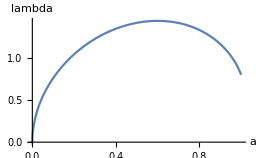

```mathematica
pars={f1->1,f2->9,x->0.2};
N[aStar/.pars]
Plot[{Lx/.pars},{a,0,1},AxesLabel->{a,lambda}]
```

Now visualize aStar as function of f2, also plotting relative proportion of age 1 individuals at stable age distribution (p1 = r/(1+r)).

```mathematica
rStar=Simplify[(f1 s1+√(s1 (f1^2 s1+4 f2 s2)))/(2 s2)/.{s1->(1-x)a,s2->(1-x)(1-a)}/.a->aStar,0<x<1]
```

-f2/(f1-√f2)

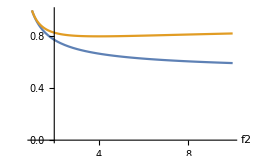

```mathematica
pars={f1->1,x->0.1};
Plot[{aStar/.pars,rStar/(1+rStar)/.pars},{f2,1,10},PlotRange->{All,{0,1}},AxesLabel->{f2}]
```

Expected lifespan in this model

```mathematica
ell=s1(1-s2)+2 s1 s2;
```

```mathematica
FullSimplify[ell]
```

s1 (1+s2)

```mathematica
ellv=FullSimplify[ell/.{s1->(1-x)a,s2->(1-x)(1-a)},{f1>0,f2>0,0<x<1}]
```

-a (2+a (-1+x)-x) (-1+x)

```mathematica
Simplify[s1 s2/.{s1->(1-x)a,s2->(1-x)(1-a)}]
```

-(-1+a) a (-1+x)^2

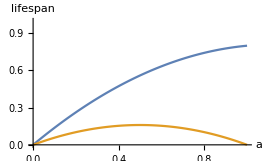

```mathematica
pars={f1->1,x->0.2};
Plot[{ellv/.pars,s1 s2/.{s1->(1-x)a,s2->(1-x)(1-a)}/.pars},{a,0,1},PlotRange->{All,{0,1}},AxesLabel->{a,lifespan}]
```

```mathematica
ellStar=FullSimplify[ell/.{s1->(1-x)a,s2->(1-x)(1-a)}/.a->aStar,{f1>0,f2>0,0<x<1}]
```

(√f2 (√f2 (-3+x)-f1 (-2+x)) (-1+x))/(f1-2 √f2)^2

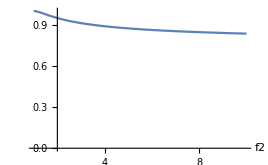

```mathematica
pars={f1->1,x->0};
Plot[{ellStar/.pars},{f2,1,10},PlotRange->{All,{0,1}},AxesLabel->{f2}]
```

Average age in a population

```mathematica
reff=Simplify[(f1 s1+√(s1 (f1^2 s1+4 f2 s2)))/(2 s2)/.{s1->(1-x)a,s2->(1-x)(1-a)}]
```

(a f1+√(a (a f1^2+4 f2-4 a f2) (-1+x)^2)-a f1 x)/(2-2 a-2 x+2 a x)

```mathematica
p1=Simplify[reff/(1+reff)]
```

(√(a (a (f1^2-4 f2)+4 f2) (-1+x)^2)+a (f1-f1 x))/(2-a (-2+f1) (-1+x)+√(a (a f1^2+4 f2-4 a f2) (-1+x)^2)-2 x)

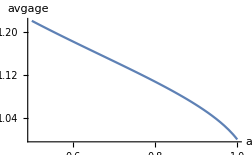

```mathematica
pars={f1->1,f2->9,x->0.1};
Plot[{p1+(1-p1)2/.pars},{a,1/2,1},AxesLabel->{a,avgage}]
```

```mathematica
p1Star=Simplify[p1/.a->aStar];
```

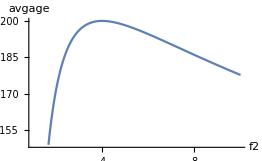

```mathematica
pars={f1->1,x->0.1};
Plot[{p1Star+(1-p1Star)2/.pars},{f2,1,10},AxesLabel->{f2,avgage}]
```

This increases and then decreases, because if f2 is very large, fertility pumps many new age 1 into pop. This makes a bottom-heavy population with lower average age.

#### Exogenous mortality with density dependence

Now with density dependent fertility. We can use the same lambda as before and introduce declining fertiity for all age classes, as population increases. This will result in a stable population size, so that lambda=1 always in long run. However, different values of a really do compete to replace one another now.

As before:

```mathematica
L=1/2 (f1 s1+√(s1 (f1^2 s1+4 f2 s2)));
```

```mathematica
Lx=L/.{s1->(1-x) a,s2->(1-x)(1-a)};
```

Now substitute in fertility functions :

```mathematica
Ld=FullSimplify[Lx/.{f1->b1 F[n],f2->b2 F[n]}/.F[n]->Exp[-k n],{0<a<1,b2>b1>0,n>0,0<x<1,k>0}]
```

-1/2 ⅇ^(-k n) (a b1+√(a (a b1^2-4 (-1+a) b2 ⅇ^(k n)))) (-1+x)

What is steady state n, for values of other variables? This means which n makes lambda==1.

```mathematica
Simplify[Reduce[{Ld==1,0<x<1,0<a<1,b1>0,b2>0,k>0},n,Reals],{0<x<1,0<a<1,b1>0,b2>0,k>0}]
```

k n==Log[-a (b1+(-1+a) b2 (-1+x)) (-1+x)]

```mathematica
nHat=Log[-a (b1+(-1+a) b2 (-1+x)) (-1+x)]/k;
```

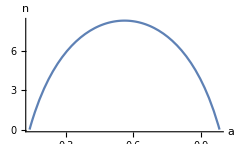

```mathematica
pars={b1->1,b2->9,x->0.1,k->0.1};
Plot[nHat/.pars,{a,0,1},PlotRange->{All,{0,All}},AxesLabel->{a,n}]
```

```mathematica
Solve[D[nHat/.pars,a]==0,a]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→0.561728}}

Again solve for optimal a, by finding value of a that maximizes population size at steady state:

```mathematica
Simplify[Reduce[{D[nHat,a]==0,k>0,n>0,b1>0,b2>0,0<x<1,0<a<1},a,Reals],{k>0,n>0,b1>0,b2>0,0<x<1,0<a<1}]
```

b2>b1+b2 x&&b1+(-1+2 a) b2 (-1+x)==0

```mathematica
aStar3sol=Solve[b1+(-1+2 a) b2 (-1+x)==0,a]
```

{{a→(-b1-b2+b2 x)/(2 b2 (-1+x))}}

```mathematica
aStar3=FullSimplify[a/.aStar3sol]
```

{(b1+b2-b2 x)/(2 b2-2 b2 x)}

Can also solve by constaining lambda=1 and solving for nHat at same time:

```mathematica
Simplify[Reduce[{D[Ld,a]==0,Ld==1,k>0},{a,n},Reals],{b2>b1>0,0<x<1,k>0}]
```

(a==1&&k n==Log[b1^2/b2]&&b1+b2 x==b2)||(k n==Log[(b1+b2-b2 x)^2/(4 b2)]&&b1+(-1+2 a) b2 (-1+x)==0&&b1+b2 x≠b2)

```mathematica
FullSimplify[Solve[b1+(-1+2 a) b2 (-1+x)==0,a],{b2>b1>0,0<x<1}]
```

{{a→(b1+b2-b2 x)/(2 b2-2 b2 x)}}

The extrinsic mortality x appears now. Plot optimal a as function of x

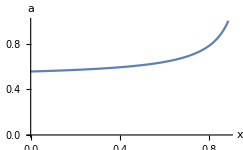

```mathematica
pars={b1->1,b2->9};
Plot[{(b1+b2-b2 x)/(2 b2-2 b2 x)/.pars},{x,0,1},PlotRange->{All,{0,1}},AxesLabel->{x,a}]
```

#### Exogenous mortality with density dependence on survival

Version of the previous model in which population size reduces survival, not fertility.

```mathematica
L=1/2 (f1 s1+√(s1 (f1^2 s1+4 f2 s2)));
```

```mathematica
Lx=L/.{s1->(1-x) a F[n],s2->(1-x)(1-a)F[n]};
```

Now substitute in survival functions :

```mathematica
Ld2=FullSimplify[Lx/.F[n]->Exp[-k n],{0<a<1,f2>f1>0,n>0,0<x<1,k>0}]
```

-1/2 ⅇ^(-k n) (a f1+√(a (a (f1^2-4 f2)+4 f2))) (-1+x)

```mathematica
Simplify[Reduce[{Ld2==1,0<x<1,0<a<1,f1>0,f2>0,k>0},n,Reals],{0<x<1,0<a<1,f1>0,f2>0,k>0}]
```

k n==Log[-1/2 (a f1+√(a (a f1^2+4 f2-4 a f2))) (-1+x)]

```mathematica
nHat=Log[-1/2 (a f1+√(a (a f1^2+4 f2-4 a f2))) (-1+x)]/k;
```

```mathematica
Simplify[Reduce[{D[nHat,a]==0,f2>f1>0},a,Reals],{f1>0,f2>f1,k>0}]
```

(a+(2 f2)/(f1^2-4 f2)==(f1 √f2)/Abs[f1^2-4 f2]&&(f1≤4||4 f2>f1^2))||(a+(2 f2)/(f1^2-4 f2)+(f1 √f2)/Abs[f1^2-4 f2]==0&&f1>4&&f1^2>4 f2)

```mathematica
aStar4=a/.Solve[a+(2 f2)/(f1^2-4 f2)==(f1 √f2)/Abs[f1^2-4 f2],a]
```

{-(2 f2)/(f1^2-4 f2)+(f1 √f2)/Abs[f1^2-4 f2]}

```mathematica
FullSimplify[(2 f2)/(-f1^2+4 f2)+(f1 √f2)/(4 f2-f1^2)]
```

1/(2-f1/(√f2))

Now x is absent from solution.

#### Implicit differentiation of age effects

Condition for stability of a:

```mathematica
dL/ds1 ds1/da+dL/ds2 ds2/da==0
```

And Euler-Lotka in our example:

```mathematica
lambda^(-2)s1 s2 f2+lambda^(-1)s1 f1==1
```